# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

## Chapter 6: Transcriptomics Examples

## Transcriptomic Analysis

## Golub ALL AML Training Set

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
golubALLAMLTrain=Import["Golub_data_set_ALL_AML_train.tsv","TSV"];
```

```mathematica
golubALLAMLTrain//Short[#,10]&
```

{{Gene Description,Gene Accession Number,1,call,2,call,3,call,4,call,5,call,6,call,7,call,8,call,9,call,10,call,11,call,12,call,13,call,14,call,15,call,16,call,17,call,18,call,19,call,20,call,21,call,22,call,23,call,24,call,25,call,26,call,27,call,34,call,35,call,36,call,37,call,38,call,28,call,29,call,30,call,31,call,32,call,33,call},«7128»,{GB DEF = mRNA (clone 1A7),Z78285_f_at,-37,A,-14,A,-41,A,-91,A,-25,A,-53,A,-42,A,20,A,-39,A,«38»,-67,A,23,A,-33,A,0,A,-46,A,-2,A,-31,A,-32,A,-3,A,-10,A}}

```mathematica
positionsTrain=Flatten@Position[golubALLAMLTrain[[1]],x_/;x≠ "call"]
```

{1,2,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77}

```mathematica
golubALLAMLTrainData=golubALLAMLTrain[[All,positionsTrain]];
```

```mathematica
golubALLAMLTrainData[[1;;3]]
```

{{Gene Description,Gene Accession Number,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,34,35,36,37,38,28,29,30,31,32,33},{AFFX-BioB-5_at (endogenous control),AFFX-BioB-5_at,-214,-139,-76,-135,-106,-138,-72,-413,5,-88,-165,-67,-92,-113,-107,-117,-476,-81,-44,17,-144,-247,-74,-120,-81,-112,-273,-20,7,-213,-25,-72,-4,15,-318,-32,-124,-135},{AFFX-BioB-M_at (endogenous control),AFFX-BioB-M_at,-153,-73,-49,-114,-125,-85,-144,-260,-127,-105,-155,-93,-119,-147,-72,-219,-213,-150,-51,-229,-199,-90,-321,-263,-150,-233,-327,-207,-100,-252,-20,-139,-116,-114,-192,-49,-79,-186}}

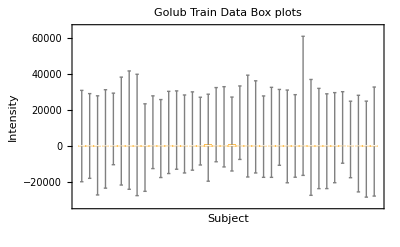

```mathematica
BoxWhiskerChart[
Transpose[N[golubALLAMLTrainData[[2;;,3;;]]]],
PlotLabel->"Golub Train Data Box plots",
FrameLabel-> {"Subject","Intensity"}]
```

### Golub Original Set Normalization

```mathematica
golubALLAMLTrainDataReplaced=(golubALLAMLTrainData[[2;;,3;;]]/.x_/; x<100 -> 100)/.x_/;x>16000-> 16000;
```

```mathematica
golubALLAMLTrainDataReplaced[[1;;3]]
```

{{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100},{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100},{100,100,100,265,100,215,238,100,106,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,136,124,100,100,100,100,100,100,100}}

```mathematica
golubTrainIDs=golubALLAMLTrainData[[2;;,1;;2]];
```

```mathematica
golubTrainIDs//Short
```

{{AFFX-BioB-5_at (endogenous control),AFFX-BioB-5_at},«7127»,{GB …1A7),…}}

```mathematica
locationsForSignalsTrain=Flatten@Position[x_/;((Max[x]-Min[x])>500 && (Max[x]/Min[x]>5))]@golubALLAMLTrainDataReplaced;
```

```mathematica
Length[locationsForSignalsTrain]
```

3051

```mathematica
golubTrainFiltered=golubALLAMLTrainDataReplaced[[locationsForSignalsTrain]];
```

```mathematica
golubTrainNormed=Transpose[Standardize[Log10[N[#]]]&/@Transpose[golubTrainFiltered]];
```

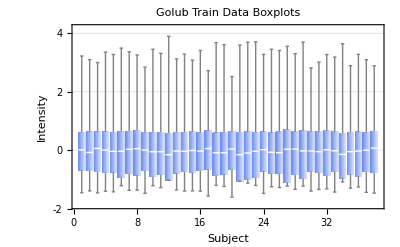

```mathematica
BoxWhiskerChart[Transpose[golubTrainNormed],
PlotLabel->"Golub Train Data Boxplots",
FrameLabel-> {"Subject","Intensity"},
PlotTheme->"Business"]
```

```mathematica
golubTrainNormedIds=golubTrainIDs[[locationsForSignalsTrain]];
```

```mathematica
golubALLAMLTrainData[[1,3;;]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,34,35,36,37,38,28,29,30,31,32,33}

```mathematica
golubPhenotypeData=<<"golubPhenotypeData";
```

```mathematica
golubPhenotypeData[[1;;3]]
```

<|Samples→{ALL/AML,BM/PB,T/B-cell (if ALL),FAB (if AML),Date,Gender,%Blasts,Treatment Response,PS,Source},1→{ALL,BM,B-cell,Missing[],9/4/1996,M,Missing[],Missing[],1.,DFCI},2→{ALL,BM,T-cell,Missing[],Missing[],M,Missing[],Missing[],0.41,DFCI}|>

```mathematica
golubPhenotypeData[["Samples"]]
```

{ALL/AML,BM/PB,T/B-cell (if ALL),FAB (if AML),Date,Gender,%Blasts,Treatment Response,PS,Source}

```mathematica
golubTrainClass=Query[1;;39,1]@golubPhenotypeData
```

<|Samples→ALL/AML,1→ALL,2→ALL,3→ALL,4→ALL,5→ALL,6→ALL,7→ALL,8→ALL,9→ALL,10→ALL,11→ALL,12→ALL,13→ALL,14→ALL,15→ALL,16→ALL,17→ALL,18→ALL,19→ALL,20→ALL,21→ALL,22→ALL,23→ALL,24→ALL,25→ALL,26→ALL,27→ALL,28→AML,29→AML,30→AML,31→AML,32→AML,33→AML,34→AML,35→AML,36→AML,37→AML,38→AML|>

### Golub ALL AML Combined Dataset

```mathematica
golubTestingClass=Query[40;;,1]@golubPhenotypeData
```

<|39→ALL,40→ALL,41→ALL,42→ALL,43→ALL,44→ALL,45→ALL,46→ALL,47→ALL,48→ALL,49→ALL,50→AML,51→AML,52→AML,53→AML,54→AML,55→ALL,56→ALL,57→AML,58→AML,59→ALL,60→AML,61→AML,62→AML,63→AML,64→AML,65→AML,66→AML,67→ALL,68→ALL,69→ALL,70→ALL,71→ALL,72→ALL|>

```mathematica
golubALLAMLIndependent=Import["Golub_data_set_ALL_AML_independent.tsv","TSV"];
positionsIndependent=Flatten@Position[golubALLAMLIndependent[[1]],x_/;x≠ "call"];
golubALLAMLIndependentData=golubALLAMLIndependent[[All,positionsIndependent]];
golubALLAMLIndependentDataReplaced=(golubALLAMLIndependentData[[2;;,3;;]]/.x_/; x<100 -> 100)/.x_/;x>16000-> 16000;
golubIndependentIDs=golubALLAMLIndependentData[[2;;,1;;2]];
```

```mathematica
golubIndependentIDs==golubTrainIDs
```

True

```mathematica
Dimensions@golubALLAMLIndependentDataReplaced
```

{7129,34}

```mathematica
Dimensions@golubALLAMLTrainDataReplaced
```

{7129,38}

```mathematica
?Join
```

Join[list_1,list_2,…] concatenates lists or other expressions that share the same head.
Join[list_1,list_2,…,n] joins the objects at level n in each of the list_i.

```mathematica
golubALLAMLDataJoined=Join[golubALLAMLTrainDataReplaced,golubALLAMLIndependentDataReplaced,2];
```

```mathematica
Dimensions[golubALLAMLDataJoined]
```

{7129,72}

```mathematica
locationsForSignalsJoined=Flatten@Position[x_/;((Max[x]-Min[x])>500 && (Max[x]/Min[x]>5))]@golubALLAMLDataJoined;
```

```mathematica
golubFiltered=golubALLAMLDataJoined[[locationsForSignalsJoined]];
```

```mathematica
golubNormed=Transpose[Standardize[Log10[N[#]]]&/@Transpose[golubFiltered]];
```

```mathematica
Dimensions[golubNormed]
```

{3571,72}

```mathematica
golubNormedIDs=golubIndependentIDs[[locationsForSignalsJoined]];
```

```mathematica
golubSampleIDs=Join[golubALLAMLTrainData[[1,3;;]],golubALLAMLIndependentData[[1,3;;]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,34,35,36,37,38,28,29,30,31,32,33,39,40,42,47,48,49,41,43,44,45,46,70,71,72,68,69,67,55,56,59,52,53,51,50,54,57,58,60,61,65,66,63,64,62}

```mathematica
golubClass=Query[Key[#]&/@golubSampleIDs,1]@golubPhenotypeData
```

<|1→ALL,2→ALL,3→ALL,4→ALL,5→ALL,6→ALL,7→ALL,8→ALL,9→ALL,10→ALL,11→ALL,12→ALL,13→ALL,14→ALL,15→ALL,16→ALL,17→ALL,18→ALL,19→ALL,20→ALL,21→ALL,22→ALL,23→ALL,24→ALL,25→ALL,26→ALL,27→ALL,34→AML,35→AML,36→AML,37→AML,38→AML,28→AML,29→AML,30→AML,31→AML,32→AML,33→AML,39→ALL,40→ALL,42→ALL,47→ALL,48→ALL,49→ALL,41→ALL,43→ALL,44→ALL,45→ALL,46→ALL,70→ALL,71→ALL,72→ALL,68→ALL,69→ALL,67→ALL,55→ALL,56→ALL,59→ALL,52→AML,53→AML,51→AML,50→AML,54→AML,57→AML,58→AML,60→AML,61→AML,65→AML,66→AML,63→AML,64→AML,62→AML|>

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

```mathematica
Query[Select[#=="AML"&]/*Keys]@golubClass
```

{34,35,36,37,38,28,29,30,31,32,33,52,53,51,50,54,57,58,60,61,65,66,63,64,62}

```mathematica
Query[Select[#=="ALL"&]/*Keys]@golubClass
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,39,40,42,47,48,49,41,43,44,45,46,70,71,72,68,69,67,55,56,59}

```mathematica
Tally[golubClass]
```

{{ALL,47},{AML,25}}

```mathematica
Position[golubNormedIDs,x_/; StringContainsQ[x,"U22376"],{2},Heads-> False]
```

{{2911,2}}

```mathematica
golubNormedIDs[[2911]]
```

{C-myb gene extracted from Human (c-myb) gene, complete primary cds, and five complete alternatively spliced cds,U22376_cds2_s_at}

```mathematica
golubNormed[[2911]]
```

{1.71002,0.773188,1.88837,2.32075,1.87385,2.02271,2.04337,2.13613,1.68993,1.37129,1.74838,0.630459,2.08134,1.13712,2.12751,2.1689,2.05944,1.17697,2.14585,1.86482,3.06356,2.52905,2.08468,2.32105,1.47215,1.95209,1.90282,0.87523,0.875575,-0.075546,-0.781754,0.419801,0.471177,1.32368,0.0314873,0.0159155,0.675457,-0.406858,1.51835,1.32106,1.49333,1.98039,2.24898,1.56569,2.37146,2.23193,2.23863,2.0087,2.08052,1.89405,-0.1543,1.10945,2.41711,2.01153,1.1975,1.24516,1.66756,2.51198,0.225917,1.40227,-0.00831519,0.92578,1.65879,2.07047,0.36254,1.98684,0.793666,0.194616,0.987969,0.0266237,1.54799,-0.0505007}

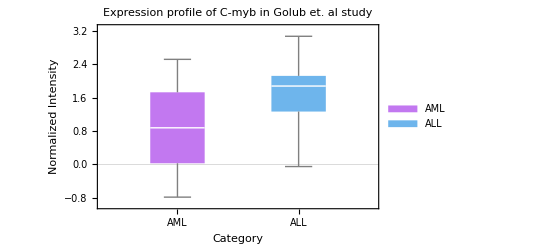

```mathematica
BoxWhiskerChart[#,PlotTheme-> "Scientific",
ChartStyle->"Pastel",
FrameLabel->{ "Category","Normalized Intensity"},
PlotLabel->
"Expression profile of C-myb in Golub et. al study",
ChartLabels->{"AML","ALL"},
ChartLegends->{"AML","ALL"}]&@{golubNormed[[2911]][[Query[Select[#=="AML"&]/*Keys]@golubClass]],golubNormed[[2911]][[Query[Select[#=="ALL"&]/*Keys]@golubClass]]}
```

```mathematica
golubAssociation=<|"AML"-> AssociationThread[golubNormedIDs[[All,2]],golubNormed[[All,Flatten@Position["AML"]@Values@golubClass]]],"ALL"-> AssociationThread[golubNormedIDs[[All,2]],golubNormed[[All,Flatten@Position["ALL"]@Values@golubClass]]]|>;
```

```mathematica
golubAssociation//Short
```

<|AML→<|AFFX-BioDn-3_at→{-1.31426,«23»,-«19»},«3569»,M…t→«1»|>,«1»|>

```mathematica
Query[All,"AFFX-BioDn-3_at"]@golubAssociation
```

<|AML→{-1.31426,-1.21439,-1.36559,-1.31182,-1.29915,-1.38573,-1.06345,-0.301638,-1.22849,-1.40419,-1.43473,0.230166,-1.44362,-1.22702,-1.28071,-1.32727,-1.05801,-1.2241,-0.266702,-0.443805,-1.14316,-1.01868,-1.42036,-1.48163,-1.3111},ALL→{-0.78835,-1.33516,-1.4235,-0.941616,-1.37342,-1.19283,-1.08886,-1.33541,-1.42439,-0.104142,-1.24374,-1.01377,-1.31832,-1.35606,-1.33969,-0.585923,-1.51022,-1.17998,-1.20761,-0.58472,-1.04577,-1.1116,-1.18712,-1.43465,-1.21717,-1.24631,0.11392,-1.22521,-0.0170479,-1.24638,-1.27091,-1.43155,0.391399,-1.14543,-1.19663,-1.07245,-1.06248,-1.12033,-1.0413,-1.21065,-1.29024,-1.06932,-1.42247,-1.18331,0.089294,-0.762898,0.0807061}|>

```mathematica
golubOmicsObject=AssociationThread[golubSampleIDs-> (AssociationThread[golubNormedIDs[[All,2]] ,{{#},{"NA"}}&/@#]&/@Transpose[golubNormed])];
```

```mathematica
Query[Key[62]]@golubOmicsObject//Short
```

<|AFFX-BioDn-3_at→{{-1.3111},{NA}},«3569»,M71243_f_at→«1»|>

```mathematica
Query[62]@golubOmicsObject//Short
```

<|AFFX-BioDn-3_at→{{-1.28071},{NA}},«3569»,M71243_f_at→«1»|>

### Golub Annotations

```mathematica
SystemOpen["https://www.affymetrix.com/analysis/index.affx"]
```

```mathematica
hu6800Genes=Import["Hu6800_Genes.tsv","TSV","Numeric"->False];
```

```mathematica
hu6800Genes[[1;;3]]
```

{{Probe Set ID,Gene Symbol,Gene Title,Entrez Gene ID,Cytoband},{AB000409_at,MKNK1,MAP kinase interacting serine/threonine kinase 1,8569,1p33},{AB000410_s_at,OGG1,8-oxoguanine DNA glycosylase,4968,3p26.2}}

```mathematica
hu6800IDtoAnnotation=AssociationThread[hu6800Genes[[All,1]],hu6800Genes[[All,2;;]]];
```

```mathematica
Query[1;;10]@hu6800IDtoAnnotation
```

<|Probe Set ID→{Gene Symbol,Gene Title,Entrez Gene ID,Cytoband},AB000409_at→{MKNK1,MAP kinase interacting serine/threonine kinase 1,8569,1p33},AB000410_s_at→{OGG1,8-oxoguanine DNA glycosylase,4968,3p26.2},AB000450_at→{VRK2,vaccinia related kinase 2,7444,2p16.1},AB000816_s_at→{ARNTL,aryl hydrocarbon receptor nuclear translocator-like,406,11p15},AB002365_at→{PRUNE2,prune homolog 2 (Drosophila),158471,9q21.2},AB002382_at→{CTNND1 /// TMX2-CTNND1,catenin (cadherin-associated protein), delta 1 /// TMX2-CTNND1 readthrough (NMD candidate),1500 /// 100528016,11q11},AB003177_at→{PSMD9,proteasome 26S subunit, non-ATPase 9,5715,12q24.31-q24.32},AB003698_at→{CDC7,cell division cycle 7,8317,1p22},AB006190_at→{AQP7,aquaporin 7,364,9p13}|>

```mathematica
Query[1;;10,StringSplit[#," /// "]&]@hu6800IDtoAnnotation
```

<|Probe Set ID→{{Gene Symbol},{Gene Title},{Entrez Gene ID},{Cytoband}},AB000409_at→{{MKNK1},{MAP kinase interacting serine/threonine kinase 1},{8569},{1p33}},AB000410_s_at→{{OGG1},{8-oxoguanine DNA glycosylase},{4968},{3p26.2}},AB000450_at→{{VRK2},{vaccinia related kinase 2},{7444},{2p16.1}},AB000816_s_at→{{ARNTL},{aryl hydrocarbon receptor nuclear translocator-like},{406},{11p15}},AB002365_at→{{PRUNE2},{prune homolog 2 (Drosophila)},{158471},{9q21.2}},AB002382_at→{{CTNND1,TMX2-CTNND1},{catenin (cadherin-associated protein), delta 1,TMX2-CTNND1 readthrough (NMD candidate)},{1500,100528016},{11q11}},AB003177_at→{{PSMD9},{proteasome 26S subunit, non-ATPase 9},{5715},{12q24.31-q24.32}},AB003698_at→{{CDC7},{cell division cycle 7},{8317},{1p22}},AB006190_at→{{AQP7},{aquaporin 7},{364},{9p13}}|>

### Leukemia Differential Expression Analysis

```mathematica
golubDifferentialSet=Merge[{golubAssociation["AML"],golubAssociation["ALL"]},Identity];
```

```mathematica
Query["AFFX-BioDn-3_at"]@golubDifferentialSet
```

{{-1.31426,-1.21439,-1.36559,-1.31182,-1.29915,-1.38573,-1.06345,-0.301638,-1.22849,-1.40419,-1.43473,0.230166,-1.44362,-1.22702,-1.28071,-1.32727,-1.05801,-1.2241,-0.266702,-0.443805,-1.14316,-1.01868,-1.42036,-1.48163,-1.3111},{-0.78835,-1.33516,-1.4235,-0.941616,-1.37342,-1.19283,-1.08886,-1.33541,-1.42439,-0.104142,-1.24374,-1.01377,-1.31832,-1.35606,-1.33969,-0.585923,-1.51022,-1.17998,-1.20761,-0.58472,-1.04577,-1.1116,-1.18712,-1.43465,-1.21717,-1.24631,0.11392,-1.22521,-0.0170479,-1.24638,-1.27091,-1.43155,0.391399,-1.14543,-1.19663,-1.07245,-1.06248,-1.12033,-1.0413,-1.21065,-1.29024,-1.06932,-1.42247,-1.18331,0.089294,-0.762898,0.0807061}}

```mathematica
Length[golubDifferentialSet]
```

3571

```mathematica
LocationTest[Query["AFFX-BioDn-3_at"]@golubDifferentialSet,Automatic,{"TestDataTable",All}]
```

| Statistic | P-Value
Mann-Whitney | 467. | 0.155795

```mathematica
LocationTest[Query["AFFX-BioDn-3_at"]@golubDifferentialSet,Automatic,"TestConclusion"]
```

The null hypothesis that the mean difference is 0 is not rejected at the 5 percent level based on the Mann-Whitney test.

```mathematica
testGolubConclusions=Query[All,LocationTest[#,Automatic,{"PValue","ShortTestConclusion"}]&]@golubDifferentialSet;
```

```mathematica
testGolubConclusions[[1;;3]]
```

<|AFFX-BioDn-3_at→{0.155795,Do not reject},AFFX-BioB-5_st→{0.705063,Do not reject},AFFX-HUMISGF3A/M97935_MA_at→{0.139275,Do not reject}|>

```mathematica
Length[#]&/@GroupBy[testGolubConclusions,Last]
```

<|Do not reject→2151,Reject→1420|>

```mathematica
testGolubConclusionsBFCorrected=Query[All,LocationTest[#,Automatic,{"PValue","ShortTestConclusion"},SignificanceLevel->(0.05/3571)]&]@golubDifferentialSet;
```

```mathematica
Length[#]&/@GroupBy[testGolubConclusionsBFCorrected,Last]
```

<|Do not reject→3312,Reject→259|>

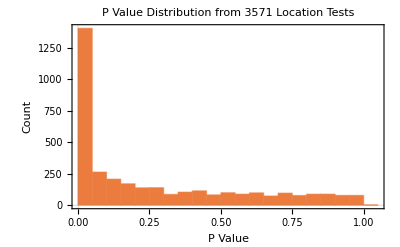

```mathematica
Histogram[
testGolubConclusionsBFCorrected[[All,1]],
PlotTheme->"Scientific",PlotLabel->
"P Value Distribution from 3571 Location Tests",
FrameLabel-> {"P Value", "Count"}]
```

```mathematica
<<MathIOmica`
```

MathIOmica (http://mathiomica.org), by [G. Mias Lab](http://georgemias.org).

```mathematica
?BenjaminiHochbergFDR
```

BenjaminiHochbergFDR[pValues] calculates for a list of pValues the Benjamini Hochberg approach false discovery rates (FDR).

```mathematica
testGolubFDRResults=BenjaminiHochbergFDR[Values@testGolubConclusionsBFCorrected[[All,1]],SignificanceLevel-> 0.05];
```

```mathematica
Keys@testGolubFDRResults
```

{Results,p-Value Cutoff,q-Value Cutoff}

```mathematica
Query["Results",1;;5]@testGolubFDRResults
```

{{0.155795,0.293585,False},{0.705063,0.818524,False},{0.139275,0.270638,False},{0.524368,0.678947,False},{0.870155,0.925901,False}}

```mathematica
testGolubFDRResults["p-Value Cutoff"]
```

0.0152203

```mathematica
testGolubFDRResults["q-Value Cutoff"]
```

0.0499556

```mathematica
pValuesGolubFDR=Query["Results",(AssociationThread[Keys[testGolubConclusionsBFCorrected]-> #]&)]@testGolubFDRResults;
```

```mathematica
Query[Select[#[[3]]==True&]]@pValuesGolubFDR;
```

```mathematica
Length[%]
```

1088

```mathematica
foldsGolubData=Query[All,Mean[#[[2]]]-Mean[#[[1]]]&]@golubDifferentialSet;
```

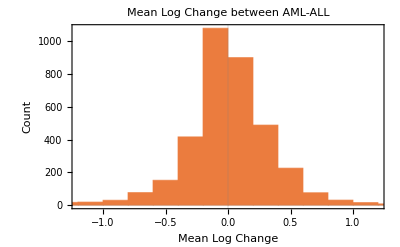

```mathematica
Histogram[foldsGolubData,
PlotTheme->"Scientific",
PlotLabel->"Mean Log Change between AML-ALL",
FrameLabel->
{"Mean Log Change","Count"}]
```

```mathematica
pValueLog10GolubData= -Log10@Query[All,2]@pValuesGolubFDR;
```

```mathematica
volcanoPlotGolubData=Merge[{foldsGolubData,pValueLog10GolubData},Identity];
```

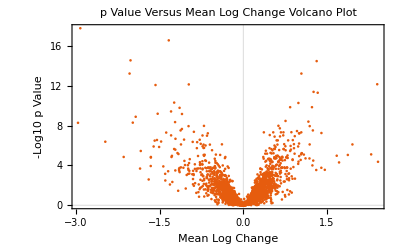

```mathematica
ListPlot[Values@volcanoPlotGolubData,
PlotTheme-> "Scientific",
PlotRange->Full,
PlotLabel-> 
"p Value Versus Mean Log Change Volcano Plot",FrameLabel->{"Mean Log Change", "-Log10 p Value"}]
```

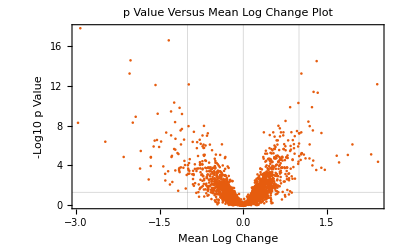

```mathematica
ListPlot[Values@volcanoPlotGolubData,
PlotTheme-> "Scientific",
PlotLabel->
 "p Value Versus Mean Log Change Plot",FrameLabel->{"Mean Log Change", "-Log10 p Value"},
PlotRange->Full,
GridLines->
{{{-1,{Red,Thick,Dashed}},0,
{1,{Red,Thick,Dashed}}},
{{-Log10[0.05],{Blue,Thick,Dashed}}}}]
```

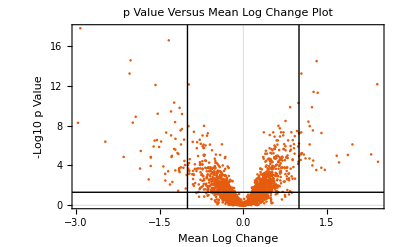

```mathematica
ListPlot[Values@volcanoPlotGolubData,
PlotTheme-> "Scientific",
PlotLabel->
 "p Value Versus Mean Log Change Plot",FrameLabel->{"Mean Log Change", "-Log10 p Value"},
PlotRange->Full,
Epilog->
{Style[ Line[{{-1,-20},{-1,20}}],
Red, Thick, Dashed],
Style[ Line[{{1,-20},{1,20}}],
Red,Thick,Dashed],
Style[ Line[{{-10,-Log10[0.05]},
{10,-Log10[0.05]}}],
Blue,Thick,Dashed]}]
```

```mathematica
selectedGenesGolub=Query[Select[Abs[#[[1]]]>1&& #[[2]]> (-Log10[0.05])&]]@volcanoPlotGolubData;
```

```mathematica
Length[selectedGenesGolub]
```

92

```mathematica
selectedGenesGolub[[1;;10]]
```

<|D10495_at→{-1.06097,6.60748},D87433_at→{-1.14956,3.48118},D88270_at→{2.29393,5.11952},D88422_at→{-2.03815,13.2644},HG1612-HT1612_at→{1.043,13.2644},HG3494-HT3688_at→{-1.29344,7.035},J03909_at→{-1.151,3.63877},J04456_at→{-1.34649,3.41742},J04615_at→{1.25548,4.49444},J04990_at→{-1.05471,4.46194}|>

```mathematica
golubSelectedGeneNames=Query[Keys@selectedGenesGolub,1]@hu6800IDtoAnnotation;
```

```mathematica
StringSplit[#," /// "]&/@Values@golubSelectedGeneNames
```

{{PRKCD},{STAB1},{VPREB1},{CSTA},{---},{---},{IFI30},{LGALS1},{SNRPN,SNURF},{CTSG},{SPTAN1},{SERPINA1},{NPY},{CYFIP2},{DNTT},{LYN},{MPO},{S100A8},{CTSA},{CD33},{CST3},{IL7R},{FCER1G},{CD81},{CD9},{LGALS3},{CSF3R},{S100A4},{CFD},{CD79B},{SPINK2},{CCND3},{CTGF},{SERPINB1},{AZU1},{NAMPT},{CD79A},{LRMP},{VCAN},{MGST1},{FHL1},{PLD3},{DPYSL2},{ANXA1},{PLEK},{SRGN},{SPI1},{PRTN3},{IGHM},{CD22},{KIAA0391,PSMA6},{RHOG},{GRN},{DGKA},{CD63},{PRDX1},{RBBP4},{TCL1A},{UPP1},{ZYX},{ATP2A3},{P4HB},{MEF2C},{CCL3,CCL3L1,CCL3L3},{CXCR4},{CD24},{MYB},{IGH,IGHA1,IGHA2},{IGHG1,IGHG2,IGHG3,IGHG4,IGHM,IGHV4-31},{LYZ},{APLP2},{LTB},{ITGB2},{CXCL8},{CXCL8},{ELANE},{ELANE},{S100A9},{CD19},{CXCL2},{IGK,IGKC,IGKV1-5,IGKV2-24},{IFI16},{CFP},{CEBPD},{STOM},{CORO1B,PTPRCAP},{LYZ},{LYZ},{LYZ},{TCF3},{RNASE2},{ITGB2}}

## Analysis of Variance for Multiple Tests

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/george/Dropbox/Documents/Workbook/CurrentProjects/Mathematica_Bioinformatics/MathematicaBioinformaticsNotebooks

```mathematica
dataSandberg=Import["sandberg-sampledata.txt","TSV"];
```

```mathematica
dataSandberg[[1;;3]]
```

{{clone,129Amygdala(1a),129Amygdala(1b),129Cerebellum(1),129Cerebellum(2),129Cortex(1),129Cortex(2),129EntorhinalCortex(1a),129EntorhinalCortex(1b),129Hippocampus(1),129Hippocampus(2),129Midbrain(1),129Midbrain(2),B6Amygdala(1a),B6Amygdala(1b),B6Cerebellum(1),B6Cerebellum(2),B6Cortex(1),B6Cortex(2),B6EntorhinalCortex(1a),B6EntorhinalCortex(1b),B6Hippocampus(1),B6Hippocampus(2),B6Midbrain(1),B6Midbrain(2)},{aa000148.s.at,298,212,258,205,220,269,167,294,218,239,220,157,257,236,256,232,240,284,236,264,188,228,241,257},{AA000151.at,243,154,228,162,192,173,191,125,99,144,186,176,127,54,202,166,135,251,185,198,102,145,202,218}}

```mathematica
Dimensions[dataSandberg]
```

{1001,25}

```mathematica
dataSandberg[[1]]
```

{clone,129Amygdala(1a),129Amygdala(1b),129Cerebellum(1),129Cerebellum(2),129Cortex(1),129Cortex(2),129EntorhinalCortex(1a),129EntorhinalCortex(1b),129Hippocampus(1),129Hippocampus(2),129Midbrain(1),129Midbrain(2),B6Amygdala(1a),B6Amygdala(1b),B6Cerebellum(1),B6Cerebellum(2),B6Cortex(1),B6Cortex(2),B6EntorhinalCortex(1a),B6EntorhinalCortex(1b),B6Hippocampus(1),B6Hippocampus(2),B6Midbrain(1),B6Midbrain(2)}

```mathematica
strains=StringCases[#,StartOfString~~_~~NumberString]&/@dataSandberg[[1]]
```

{{},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{B6},{B6},{B6},{B6},{B6},{B6},{B6},{B6},{B6},{B6},{B6},{B6}}

```mathematica
regions=StringCases[#,NumberString..~~y:WordCharacter..~~"("~~_-> y ]&/@dataSandberg[[1]]
```

{{},{Amygdala},{Amygdala},{Cerebellum},{Cerebellum},{Cortex},{Cortex},{EntorhinalCortex},{EntorhinalCortex},{Hippocampus},{Hippocampus},{Midbrain},{Midbrain},{Amygdala},{Amygdala},{Cerebellum},{Cerebellum},{Cortex},{Cortex},{EntorhinalCortex},{EntorhinalCortex},{Hippocampus},{Hippocampus},{Midbrain},{Midbrain}}

```mathematica
repeats=StringCases[#,__~~"("~~x__~~")"-> x ]&/@dataSandberg[[1]]
```

{{},{1a},{1b},{1},{2},{1},{2},{1a},{1b},{1},{2},{1},{2},{1a},{1b},{1},{2},{1},{2},{1a},{1b},{1},{2},{1},{2}}

```mathematica
dataSandberg[[2]]
```

{aa000148.s.at,298,212,258,205,220,269,167,294,218,239,220,157,257,236,256,232,240,284,236,264,188,228,241,257}

```mathematica
Transpose[{strains,regions,dataSandberg[[2]]}]//Short[#,3]&
```

{{{},{},aa000148.s.at},{{129},{Amygdala},298},«21»,{{B6},{Midbrain},241},{{B6},{Midbrain},257}}

```mathematica
Flatten[#]&/@Transpose[{strains,regions,dataSandberg[[2]]}]//Short[#,3]&
```

{{aa000148.s.at},{129,Amygdala,298},{129,Amygdala,212},«20»,{B6,Midbrain,241},{B6,Midbrain,257}}

```mathematica
<|#[[1,1]]-> #[[2;;]]|>&@(Flatten[#]&/@Transpose[{strains,regions,dataSandberg[[2]]}])//Short[#,3]&
```

<|aa000148.s.at→{{129,Amygdala,298},{129,Amygdala,212},«20»,{B6,Midbrain,241},{B6,Midbrain,257}}|>

```mathematica
associationDataSandberg=AssociationThread[#[[All,1,1]]->#[[All,2;;]]]&@( (Flatten[#]&/@Transpose[{strains,regions,#}])&/@dataSandberg);
```

```mathematica
Query[{1,29}]@associationDataSandberg
```

<|clone→{{129,Amygdala,129Amygdala(1a)},{129,Amygdala,129Amygdala(1b)},{129,Cerebellum,129Cerebellum(1)},{129,Cerebellum,129Cerebellum(2)},{129,Cortex,129Cortex(1)},{129,Cortex,129Cortex(2)},{129,EntorhinalCortex,129EntorhinalCortex(1a)},{129,EntorhinalCortex,129EntorhinalCortex(1b)},{129,Hippocampus,129Hippocampus(1)},{129,Hippocampus,129Hippocampus(2)},{129,Midbrain,129Midbrain(1)},{129,Midbrain,129Midbrain(2)},{B6,Amygdala,B6Amygdala(1a)},{B6,Amygdala,B6Amygdala(1b)},{B6,Cerebellum,B6Cerebellum(1)},{B6,Cerebellum,B6Cerebellum(2)},{B6,Cortex,B6Cortex(1)},{B6,Cortex,B6Cortex(2)},{B6,EntorhinalCortex,B6EntorhinalCortex(1a)},{B6,EntorhinalCortex,B6EntorhinalCortex(1b)},{B6,Hippocampus,B6Hippocampus(1)},{B6,Hippocampus,B6Hippocampus(2)},{B6,Midbrain,B6Midbrain(1)},{B6,Midbrain,B6Midbrain(2)}},aa013993.at→{{129,Amygdala,103},{129,Amygdala,76},{129,Cerebellum,130},{129,Cerebellum,150},{129,Cortex,130},{129,Cortex,110},{129,EntorhinalCortex,81},{129,EntorhinalCortex,92},{129,Hippocampus,87},{129,Hippocampus,111},{129,Midbrain,105},{129,Midbrain,117},{B6,Amygdala,81},{B6,Amygdala,83},{B6,Cerebellum,74},{B6,Cerebellum,63},{B6,Cortex,96},{B6,Cortex,132},{B6,EntorhinalCortex,67},{B6,EntorhinalCortex,114},{B6,Hippocampus,59},{B6,Hippocampus,44},{B6,Midbrain,100},{B6,Midbrain,95}}|>

```mathematica
lmExample=LinearModelFit[associationDataSandberg[[29]],{str,rg,str*rg},{str,rg},NominalVariables->{str,rg}]
```

FittedModel[«18»+34. «17»[«1»] DiscreteIndicator[str,129,{129,B6}]]

```mathematica
lmExample["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lmExample[{"FitResiduals","AdjustedRSquared"}]
```

{{13.5,-13.5,-10.,10.,10.,-10.,-5.5,5.5,-12.,12.,-6.,6.,-1.,1.,5.5,-5.5,-18.,18.,-23.5,23.5,7.5,-7.5,2.5,-2.5},0.612559}

```mathematica
lmExample["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
str | 1 | 3360.67 | 3360.67 | 12.905 | 0.00369748
rg | 5 | 4675.33 | 935.067 | 3.59066 | 0.0323236
rg str | 5 | 4298.33 | 859.667 | 3.30112 | 0.041804
Error | 12 | 3125. | 260.417 |  | 
Total | 23 | 15459.3 |  |  |

```mathematica
#-> lmExample[#]&/@{"AdjustedRSquared","AIC","AICc","ANOVATableDegreesOfFreedom","ANOVATableEntries","ANOVATableFStatistics","ANOVATableMeanSquares","ANOVATablePValues","ANOVATableSumsOfSquares","CoefficientOfVariation","Response","RSquared","SequentialSumOfSquares"}
```

{AdjustedRSquared→0.612559,AIC→215.604,AICc→252.004,ANOVATableDegreesOfFreedom→{1,5,5,12,23},ANOVATableEntries→{{1,3360.67,3360.67,12.905,0.00369748},{5,4675.33,935.067,3.59066,0.0323236},{5,4298.33,859.667,3.30112,0.041804},{12,3125.,260.417},{23,15459.3}},ANOVATableFStatistics→{12.905,3.59066,3.30112},ANOVATableMeanSquares→{3360.67,935.067,859.667,260.417},ANOVATablePValues→{0.00369748,0.0323236,0.041804},ANOVATableSumsOfSquares→{3360.67,4675.33,4298.33,3125.,15459.3},CoefficientOfVariation→0.168391,Response→{103,76,130,150,130,110,81,92,87,111,105,117,81,83,74,63,96,132,67,114,59,44,100,95},RSquared→0.797857,SequentialSumOfSquares→{3360.67,4675.33,4298.33}}

```mathematica
1-CDF[FRatioDistribution[Plus@@lmExample["ANOVATableDegreesOfFreedom"][[1;;-3]],lmExample["ANOVATableDegreesOfFreedom"][[-2]]],Mean[lmExample["ANOVATableFStatistics"]]]
```

0.00144074

```mathematica
<<ANOVA`
```

```mathematica
?ANOVA
```

ANOVA[data] performs a one-way analysis of variance.
ANOVA[data,model,vars] performs an analysis of variance for model as a function of the categorical variables vars.

```mathematica
ANOVA[associationDataSandberg[[29]],{str,rg,All},{str,rg},PostTests->{Tukey,Bonferroni},SignificanceLevel->.05]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
str | 1 | 3360.67 | 3360.67 | 12.905 | 0.00369748
rg | 5 | 4675.33 | 935.067 | 3.59066 | 0.0323236
rg str | 5 | 4298.33 | 859.667 | 3.30112 | 0.041804
Error | 12 | 3125. | 260.417 |  | 
Total | 23 | 15459.3 |  |  | ,CellMeans→All | 95.8333
str[129] | 107.667
str[B6] | 84.
rg[Amygdala] | 85.75
rg[Cerebellum] | 104.25
rg[Cortex] | 117.
rg[EntorhinalCortex] | 88.5
rg[Hippocampus] | 75.25
rg[Midbrain] | 104.25
rg[Amygdala] str[129] | 89.5
rg[Amygdala] str[B6] | 82.
rg[Cerebellum] str[129] | 140.
rg[Cerebellum] str[B6] | 68.5
rg[Cortex] str[129] | 120.
rg[Cortex] str[B6] | 114.
rg[EntorhinalCortex] str[129] | 86.5
rg[EntorhinalCortex] str[B6] | 90.5
rg[Hippocampus] str[129] | 99.
rg[Hippocampus] str[B6] | 51.5
rg[Midbrain] str[129] | 111.
rg[Midbrain] str[B6] | 97.5,PostTests→{str→Bonferroni | {129,B6}
Tukey | {129,B6},rg→Bonferroni | {Cortex,Hippocampus}
Tukey | {Cortex,Hippocampus}}}

```mathematica
linearModelsSandberg=Query[2;;,LinearModelFit[#,{str,rg,str*rg},{str,rg},NominalVariables->{str,rg}]&]@associationDataSandberg;
```

```mathematica
linearModelsSandberg[[1;;4]]
```

<|aa000148.s.at→FittedModel[«15»+81. «17»[«1»] DiscreteIndicator[str,129,{129,B6}]],AA000151.at→FittedModel[«18»+27. «1» DiscreteIndicator[«1»]],aa000380.s.at→FittedModel[«16»+84. «1» «1»],aa000467.s.at→FittedModel[«1»]|>

```mathematica
pValuesSandberg=Query[All,Chop[Re[#["ANOVATablePValues"]]]&]@linearModelsSandberg;
```

```mathematica
pValuesSandberg[[1;;3]]
```

<|aa000148.s.at→{0.426513,0.7229,0.782272},AA000151.at→{0.673324,0.154761,0.242283},aa000380.s.at→{0.0781434,0.825637,0.434008}|>

```mathematica
regionalOnlyGenes=Query[Select[#[[2]]<0.0001&&#[[3]]>0.1&]]@pValuesSandberg;
```

```mathematica
Length[regionalOnlyGenes]
```

41

```mathematica
Keys[regionalOnlyGenes]
```

{AA028280.at,aa028770.i.at,aa028770.s.at,aa030488.at,aa030488.g.at,AA030688.s.at,AA033074.s.at,aa033314.s.at,aa034739.s.at,aa035912.at,aa035912.g.at,AA038775.s.at,aa105755.at,aa106571.g.at,aa120563.at,aa122778.s.at,aa123328.s.at,aa123934.s.at,AA124090.i.at,aa153748.g.at,aa153942.s.at,aa155529.s.at,AA166452.at,AA171106.at,aa172673.s.at,aa172864.s.at,aa174604.s.at,aa175734.s.at,aa175767.f.at,aa178190.s.at,aa182125.s.at,aa183544.s.at,aa183623.s.at,AA189677.at,aa189989.at,AA198947.at,aa204034.s.at,aa204106.s.at,AA204584.at,aa210359.s.at,aa220788.s.at}

```mathematica
regionalOnlyGenes[[1;;3]]
```

<|AA028280.at→{0.273171,1.63919×10^-7,0.172343},aa028770.i.at→{0.404534,0.0000899459,0.602528},aa028770.s.at→{0.213727,9.20976×10^-7,0.150637}|>

```mathematica
regionFDRResults=BenjaminiHochbergFDR[Flatten[#[[All,2]]]&@Values@pValuesSandberg,SignificanceLevel-> 0.05];
```

```mathematica
Query["p-Value Cutoff"]@regionFDRResults
```

0.00940035

```mathematica
Query["q-Value Cutoff"]@regionFDRResults
```

0.0489602

```mathematica
pValuesSandbergRegionFDR=Query["Results",(AssociationThread[Keys[pValuesSandberg]-> #]&)]@regionFDRResults;
```

```mathematica
Query[Select[#[[3]]==True&]]@pValuesSandbergRegionFDR//Short
```

<|aa000750.s.at→{«1»},«190»,aa220788.s.at→{«1»}|>

```mathematica
Length[%]
```

192

```mathematica
sortedSandbergRegionFDR=Query[Select[#[[3]]==True&]/*SortBy[#[[2]]&]]@pValuesSandbergRegionFDR;
```

```mathematica
Keys@Query[1;;20]@sortedSandbergRegionFDR
```

{aa183623.s.at,aa212550.s.at,aa220788.s.at,AA171106.at,aa123328.s.at,AA189887.at,AA030688.s.at,aa137436.s.at,aa153748.g.at,AA028280.at,aa106571.g.at,aa204106.s.at,aa204034.s.at,aa172864.s.at,aa189518.s.at,AA038775.s.at,aa028770.s.at,aa123989.at,aa189989.at,aa172673.s.at}

```mathematica
dataSandbergSorted=Query[Keys@Query[1;;20]@sortedSandbergRegionFDR,All,3]@associationDataSandberg;
```

```mathematica
dataSandbergSorted[[1;;3]]
```

<|aa183623.s.at→{594,708,-15,-2,966,1165,1518,1481,137,230,81,105,726,535,-8,10,937,950,1452,1464,205,181,68,240},aa212550.s.at→{47,51,252,222,56,43,28,13,50,45,35,29,59,90,390,377,24,49,35,42,53,53,78,74},aa220788.s.at→{661,729,8,-66,622,642,587,567,726,752,447,480,781,743,12,-25,516,646,541,480,637,720,375,521}|>

```mathematica
clustersSandbergSorted=MatrixClusters[N[Standardize[#]&/@dataSandbergSorted]];
```

Agglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

```mathematica
Keys[clustersSandbergSorted]
```

{1}

```mathematica
Keys@clustersSandbergSorted["1"]
```

{RowCluster,ColumnCluster,RowSplitClusters,ColumnSplitClusters,GroupAssociationsRows,GroupAssociationsColumns}

```mathematica
clustersSandbergSorted["1","GroupAssociationsRows"]
```

<|H:G1→{aa183623.s.at,aa153748.g.at,aa172864.s.at,aa028770.s.at,aa189989.at,AA189887.at,aa204034.s.at,aa220788.s.at,AA171106.at},H:G2→{aa212550.s.at,aa204106.s.at,AA038775.s.at,aa189518.s.at,aa106571.g.at,aa123989.at,aa123328.s.at,aa172673.s.at,aa137436.s.at,AA028280.at,AA030688.s.at}|>

```mathematica
clustersSandbergSorted["1","GroupAssociationsColumns"]
```

<|V:G1→{1,2,13,14,5,6,17,18,7,8,19,20},V:G2→{21,9,10,22},V:G3→{24,23,11,12},V:G4→{15,16,3,4}|>

```mathematica
horizontalLabels=Flatten@Values@clustersSandbergSorted["1","GroupAssociationsColumns"]
```

{1,2,13,14,5,6,17,18,7,8,19,20,21,9,10,22,24,23,11,12,15,16,3,4}

```mathematica
regions=AssociationThread[Range[Length[#]]-> #]&@Query[1,All,{1,2}]@associationDataSandberg/.{"129"-> "1","B6"-> "2","Amygdala"-> "a","Cerebellum"-> "c","Cortex"-> "cx","EntorhinalCortex"-> "e","Hippocampus"-> "h","Midbrain"-> "m"}
```

<|1→{1,a},2→{1,a},3→{1,c},4→{1,c},5→{1,cx},6→{1,cx},7→{1,e},8→{1,e},9→{1,h},10→{1,h},11→{1,m},12→{1,m},13→{2,a},14→{2,a},15→{2,c},16→{2,c},17→{2,cx},18→{2,cx},19→{2,e},20→{2,e},21→{2,h},22→{2,h},23→{2,m},24→{2,m}|>

```mathematica
heatmapLabels=Values@Query[horizontalLabels,(#[[1]])/(#[[2]])&]@regions
```

{1/a,1/a,2/a,2/a,1/cx,1/cx,2/cx,2/cx,1/e,1/e,2/e,2/e,2/h,1/h,1/h,2/h,2/m,2/m,1/m,1/m,2/c,2/c,1/c,1/c}

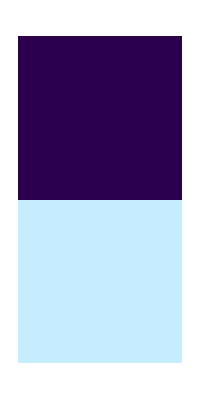
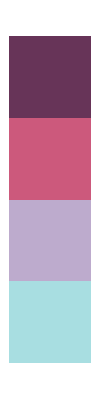
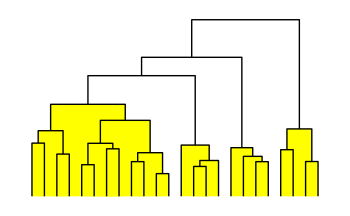
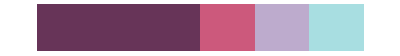
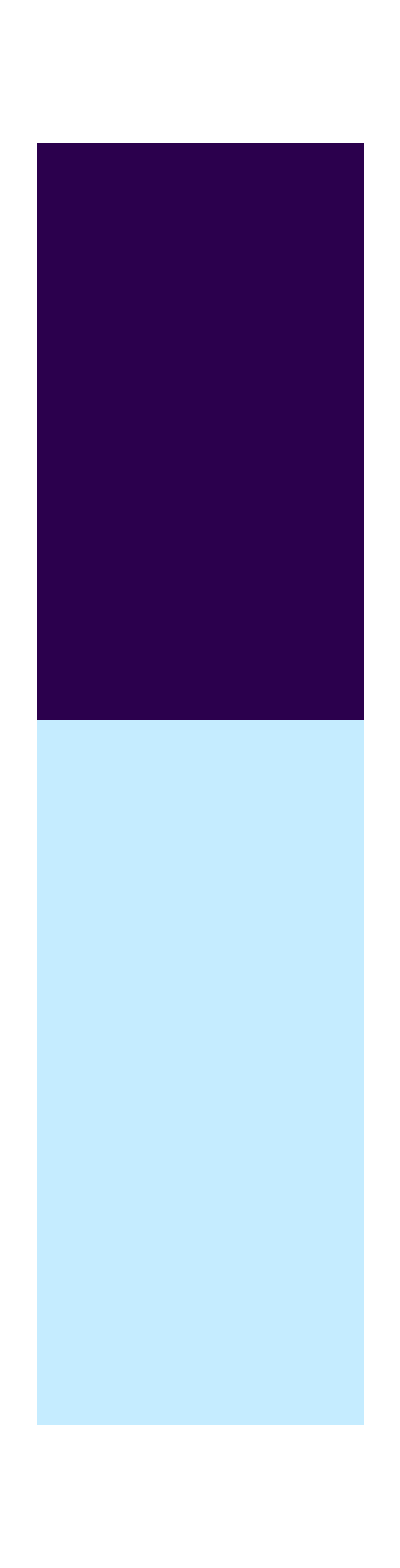
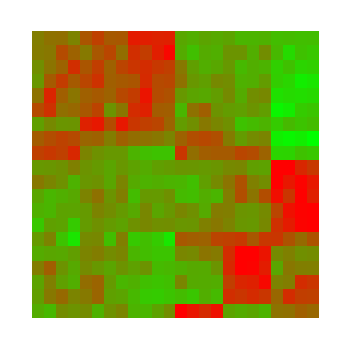
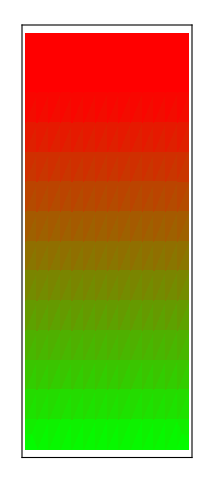
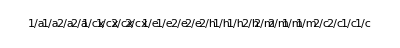
| 
Sorted Sandberg Gene Expression Data Clustering | 
GroupAssociations | 
GroupIndex→Size | 
Rows | Columns
-Graphics- | -Graphics- |  | -Graphics- |  | 
 |  | -Graphics- |  | 
-Graphics- | -Graphics- | -Graphics- |  | -Graphics-
 |  | -Graphics- |  | 
 |  | Sample Data |  |  |

```mathematica
MatrixDendrogramHeatmap[clustersSandbergSorted["1"],
FrameName->
"Sorted Sandberg Gene Expression Data Clustering",HorizontalAxisName->"Sample Data",
HorizontalLabels-> heatmapLabels,
ImageSize-> 350]
```

1	R. Sandberg, R. Yasuda, D.G. Pankratz, T.A. Carter, J.A. Del Rio, L. Wodicka, M. Mayford, D.J. Lockhart, C. Barlow, Proc. Natl. Acad. Sci. USA 97 (2000) 11038–11043.

2	 P. Pavlidis, W.S. Noble, Bioinformatics 19 (2003) 295–296.

3	Paul Pavlidis, Using ANOVA for gene selection from microarray studies of the nervous system,  Methods, Volume 31, Issue 4, 2003, Pages 282-289, ISSN 1046-202